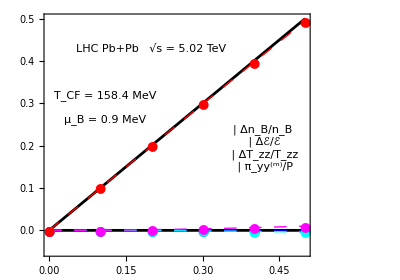

```mathematica
(* Subscript[π, xx] = - Subscript[π, yy]*)

(*LHC Pb+Pb 5.02 TeV*)

T = 158.4;
μB =0.90; 

frac=Table[0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.00040041,0.0016018,0.0036048,0.0064102,0.010019};

piyyoverPdata = {0.0,0.099952,0.19961,0.29869,0.3969,0.49395};

ΔTzzoverTzzdata = {0.0,-0.00015187,-0.00060887,-0.0013751,-0.0024575,-0.0038658};

style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};



legend1=Panel[Grid[{{Graphics[{Blue,Disk[]},ImageSize->10],Style["Δn_B/n_B",FontSize->18,FontFamily->"Times"]},{Graphics[{RGBColor[1,0,1],Disk[]},ImageSize->10],Style["Δℰ/ℰ",FontSize->18,FontFamily->"Times"]},

{Graphics[{RGBColor[0,1,1],Disk[]},ImageSize->10],Style["ΔT_zz/T_zz",FontSize->18,FontFamily->"Times"]},{Graphics[{Red,Disk[]},ImageSize->10],Style["π_yy^(m)/P",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend3=Panel[Grid[{{Style["LHC Pb+Pb   √s = 5.02 TeV",FontSize->16,FontFamily->"Times"]}}],Background->White];



legend2=Panel[Grid[{{Style["T_CF = 158.4 MeV",FontSize->16,FontFamily->"Times"]},{},{Style["μ_B = 0.9 MeV",FontSize->16,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
piyyoverPplot  = Table[{frac[[i]],piyyoverPdata [[i]]},{i,1,Length[frac]}];
ΔTzzoverTzzplot = Table[{frac[[i]],ΔTzzoverTzzdata[[i]]},{i,1,Length[frac]}];

pi1=Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.05,0.5},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,ΔTzzoverTzzplot,Δϵoverϵplot,piyyoverPplot},PlotRange->{-0.1,1},Joined->True,Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13},{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend1,{0.418,0.194}],Inset[legend2,{0.11,0.29}],Inset[legend3,{0.2,0.43}]},ImageSize->{400,300}]
```

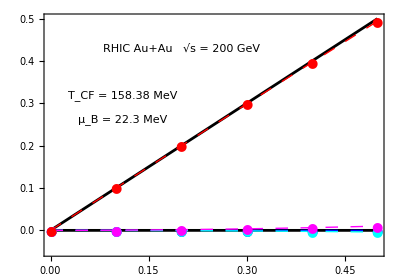

```mathematica
T = 158.384;
μB =22.3; 

frac=Table[0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.00040,0.0016005,0.0036017,0.0064047,0.010011};

piyyoverPdata = {0.0,0.099952,0.19961,0.29869,0.3969,0.49395};

ΔTzzoverTzzdata = {0.0,-0.00015186,-0.0006088,-0.0013749,-0.0024572,-0.0038653};


style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};


legend2=Panel[Grid[{{Style["T_CF = 158.38 MeV",FontSize->16,FontFamily->"Times"]},{},{Style["μ_B = 22.3 MeV",FontSize->16,FontFamily->"Times"]}}],Background->White];

legend3=Panel[Grid[{{Style["RHIC Au+Au   √s = 200 GeV",FontSize->16,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
piyyoverPplot  = Table[{frac[[i]],piyyoverPdata [[i]]},{i,1,Length[frac]}];
ΔTzzoverTzzplot = Table[{frac[[i]],ΔTzzoverTzzdata[[i]]},{i,1,Length[frac]}];

pi2=Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.05,0.5},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,ΔTzzoverTzzplot,Δϵoverϵplot,piyyoverPplot},PlotRange->{-0.1,1},Joined->True,Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13},{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend2,{0.11,0.29}],Inset[legend3,{0.2,0.43}]},ImageSize->{400,300}]
```

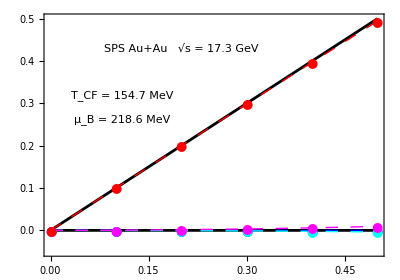

```mathematica
T = 154.7;
μB =218.6; 

frac=Table[0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.00037237,0.0014896,0.003352,0.0059602,0.009315};

piyyoverPdata = {0.0,0.099953,0.19962,0.29873,0.39698,0.4941};

ΔTzzoverTzzdata = {0.0,-0.00015019,-0.00060196,-0.001359,-0.0024273,-0.0038157};

style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};

legend2=Panel[Grid[{{Style["T_CF = 154.7 MeV",FontSize->16,FontFamily->"Times"]},{},{Style["μ_B = 218.6 MeV",FontSize->16,FontFamily->"Times"]}}],Background->White];

legend3=Panel[Grid[{{Style["SPS Au+Au   √s = 17.3 GeV",FontSize->16,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
piyyoverPplot  = Table[{frac[[i]],piyyoverPdata [[i]]},{i,1,Length[frac]}];
ΔTzzoverTzzplot = Table[{frac[[i]],ΔTzzoverTzzdata[[i]]},{i,1,Length[frac]}];

pi3=Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.05,0.5},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,ΔTzzoverTzzplot,Δϵoverϵplot,piyyoverPplot},PlotRange->{-0.1,1},Joined->True,Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13},{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend2,{0.11,0.29}],Inset[legend3,{0.2,0.43}]},ImageSize->{400,300}]
```

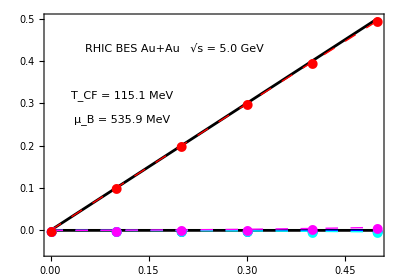

```mathematica
T = 115.1;
μB =535.9; 

frac=Table[0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.00027926,0.001117,0.0025132,0.0044678,0.0069805};

piyyoverPdata = {0.0,0.099958,0.19966,0.29886,0.39731,0.49475};

ΔTzzoverTzzdata = {0.0,-0.00013964,-0.0005593,-0.0012612,-0.0022489,-0.0035277};

style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};

legend2=Panel[Grid[{{Style["T_CF = 115.1 MeV",FontSize->16,FontFamily->"Times"]},{},{Style["μ_B = 535.9 MeV",FontSize->16,FontFamily->"Times"]}}],Background->White];

legend3=Panel[Grid[{{Style["RHIC BES Au+Au   √s = 5.0 GeV",FontSize->16,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
piyyoverPplot  = Table[{frac[[i]],piyyoverPdata [[i]]},{i,1,Length[frac]}];
ΔTzzoverTzzplot = Table[{frac[[i]],ΔTzzoverTzzdata[[i]]},{i,1,Length[frac]}];

pi4=Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.05,0.5},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7,FrameLabel->{"(T_yy-T_xx)/2P"}],
ListPlot[{ΔnBovernBplot,ΔTzzoverTzzplot,Δϵoverϵplot,piyyoverPplot},PlotRange->{-0.1,1},Joined->True,Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13},{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend2,{0.11,0.29}],Inset[legend3,{0.19,0.43}]},ImageSize->{400,300},FrameLabel->{"(T_yy-T_xx)/2P"}]
```

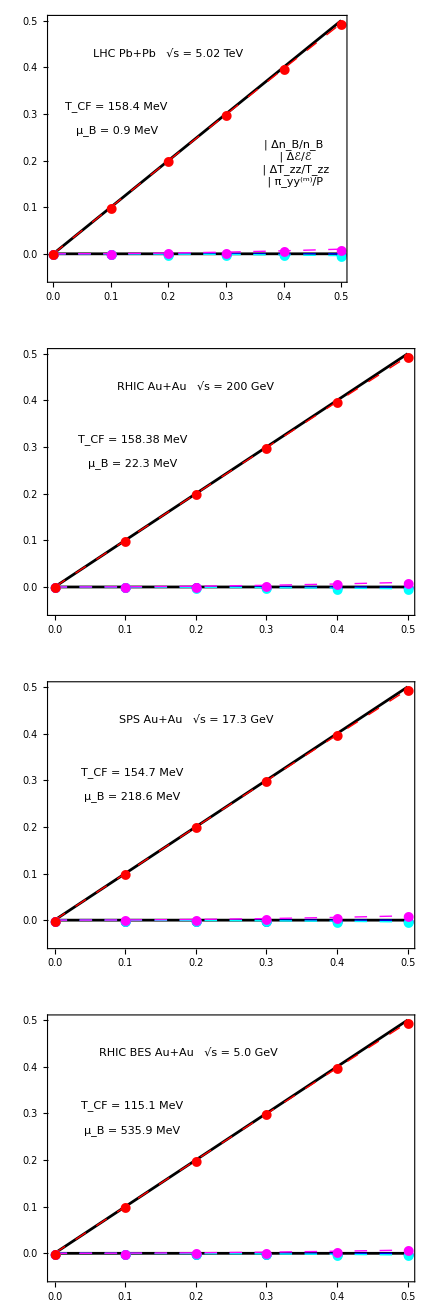

pitotal.pdf

```mathematica
pitotal=GraphicsGrid[{{pi1},{pi2},{pi3},{pi4}}]

Export["pitotal.pdf",pitotal]
```